```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
TEMP = 9.*^-9; (* GeV *)
mn     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
vd  = 270.*^3;(* ms^-1 *)
vns =  200.*^3 ;(* ms^-1 *)
hbarc = (0.1973269788*1.*^-15); (* GeV m *)
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

NSMass = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

```mathematica
avgμFn =NIntegrate[muFn[x]*x^2, {x,rMin, rMax}]/NIntegrate[x^2, {x, rMin, rMax}];
```

## Other Functions

```mathematica
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*NSMass[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*NSMass[rMax]*2.*^30)/(rMax*1.*^3)]/SOL
]; 


B[R_]:=1 - (2*G*NSMass[R*rMax]*2*^30)/(SOL^2*R*rMax*1*^3);
ve = Interpolation[Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}]];
μ[mx_]:=mx/mn;


s[mx_] :=mx^2/μ[mx]^2*(1+μ[mx]^2+2/(√B[1])*μ[mx]);
Er[ctheta_,r_, mx_]:= (mn*mx^2*γ[r]^2*ve[r]^2)/(mn^2 + mx^2 + 2*γ[r]*mx*mn)*(1 - ctheta);
jacobian[ mx_]:=B[1]*((1+μ[mx]^2+2/(√B[1])*μ[mx])/(2*(1-B[1])*mx^2));
σTot[dσ_,mx_?NumericQ]:= NIntegrate[dσ[t,mx] ,{t,-4*mx^2*((1-B[1])/(B[1]*(1+μ[mx]^2+2/(√B[1])*μ[mx]))),0}]*jacobian[mx];
```

## Differential Cross Sections

```mathematica
d1[t_, mx_]:= (mn^2*(4*mx^2-t)*(4*mx^2-μ[mx]^2*t))/(32*π*(μ[mx])^2*s[mx]);
d2[t_, mx_]:= (mn^2*t*(μ[mx]^2*t - 4*mx^2))/(32*π*s[mx]*μ[mx]^2);
d3[t_, mx_]:= (mn^2*t*(t - 4*mx^2))/(32*π*s[ mx]);
d4[t_, mx_]:= (mn^2*t^2)/(32*π*s[mx]);
d5[t_, mx_]:= (2*(μ[mx]^2+1)^2*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*s[mx]*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2))/(16*π*μ[mx]^4*s[mx]);
d6[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+μ[mx]^2*t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d7[t_, mx_]:= 1/(16*π*μ[mx]^4*s[mx])(2*(μ[mx]^2-1)^2*mx^4-4*(μ[mx]^2*s[mx] +s[mx]+t)*μ[mx]^2*mx^2+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d8[t_, mx_]:= 1/(4*π*μ[mx]^4*s[mx])(2*(μ[mx]^4+10*μ[mx]^2+1)*mx^4-4*(μ[mx]^2+1)*μ[mx]^2*mx^2*(s[mx]+t)+μ[mx]^4*(2*s[mx]^2+2*s[mx]*t+t^2));
d9[t_, mx_]:= 1/(4*π*μ[mx]^4*s[mx])(4*(μ[mx]^4+4*μ[mx]^2+1)*mx^4 - 2*(μ[mx]^2+1)*μ[mx]^2*mx^2*(4*s[mx]+t)+μ[mx]^4*(2*s[mx]+t)^2);
d10[t_, mx_]:=1/(4*π*μ[mx]^4*s[mx])(4*(μ[mx]^2-1)^2*mx^4 - 2*(μ[mx]^2+1)*μ[mx]^2*mx^2*(4*s[mx]+t)+μ[mx]^4*(2*s[mx]+t)^2);
```

## Average over angles

```mathematica
avgθ[dσ_,mx_?NumericQ]:=NIntegrate[dσ[t,mx]*(-t)*(jacobian[mx])^2 ,{t,-4*mx^2*((1-B[1])/(B[1]*(1+μ[mx]^2+2/(√B[1])*μ[mx]))),0}]/NIntegrate[dσ[t,mx]*jacobian[mx] ,{t,-4*mx^2*((1-B[1])/(B[1]*(1+μ[mx]^2+2/(√B[1])*μ[mx]))),0}];
```

```mathematica
qtr[dσ_, mx_?NumericQ]:=√(2*mn*((1-B[1])*mx*μ[mx])/(B[1] + 2*√B[1]*μ[mx] + B[1]*μ[mx]^2)*avgθ[dσ, mx]);
```

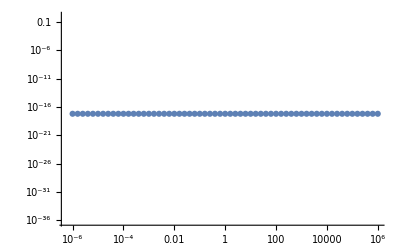

```mathematica
ListLogLogPlot[With[{x:=10^xp}, Table[{x,σTh[d1, x]}, {xp, -6, 6, 0.2}]]]
```

## Capture Rate

```mathematica
μFnAvg =NIntegrate[muFn[x]*x^2, {x,rMin, rMax}]/NIntegrate[x^2, {x,rMin, rMax}];
```

```mathematica
capGeom[dσ_, mx_]:=(π*(rMax*10^3/hbarc)^2*(1 - B[1]^2))/(vns/SOL*B[1])*(0.4*hbarc^3)/(mx*(1*^-6))*Erf[√(3/2)*vns/vd]*qtr[dσ, mx]/(√(2*mn*μFnAvg*1*^-3));
capGeomNoPB[ mx_]:=(π*(rMax*10^3)^2*(1 - B[1]^2))/(vns*B[1])*(0.4*SOL^2)/(mx*(1*^-6))*Erf[√(3/2)*vns/vd];
```

## Temperature Limits

```mathematica
B[R_]:=1 - (2*G*NSMass[R*rMax]*2*^30)/(SOL^2*R*rMax*1*^3);
σTh[dσ_,mx_]:=(π*rMax^2*1*^6*mn*1.78*^-27)/(NSMass[rMax]*2*^30)*1/(0.389*1*^-31)*((√(2*mn*μFnAvg*1*^-3))/qtr[dσ, mx])^-1;
```

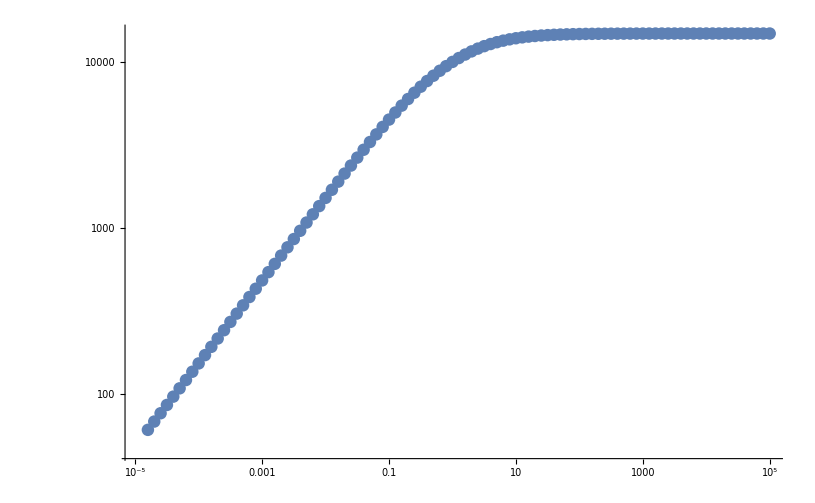

```mathematica
ListLogLogPlot[With[{x:=10^xp},ParallelTable[{x, (σTot[d1,x]/σTh[d1,x])^0.25}, {xp, -4.8,5, 0.1}]]]
```

## Capture Rates

```mathematica
Do[
Evaluate[Symbol[cap<>"CAP"]] =Interpolation[Import[StringJoin[{cap, "_cap.dat"}]]]
,
{cap, {"d0", "d1", "d2","d3","d4","d5","d6","d7", "d8", "d9", "d10"}}
]
```

```mathematica
fracCAP[dCAP_, dσ_, mx_]:=dCAP[Log10[mx]]/capGeom[dσ,mx];
fracCS[CS_, mx_]:= σTot[CS, mx]/σTh[CS, mx];
```

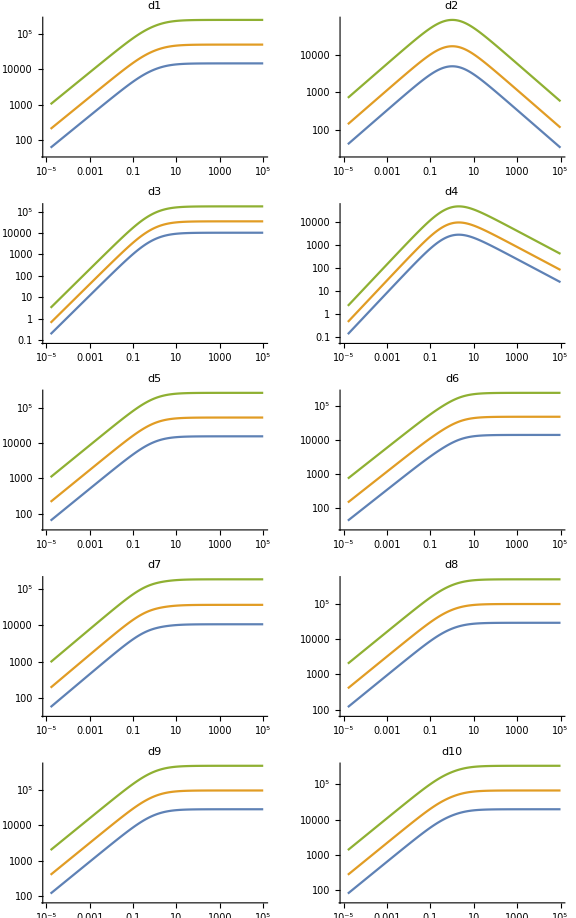

```mathematica
GraphicsGrid[Partition[Table[
ListLogLogPlot[{With[{x:=10^xp},Table[{x, (fracCS[ToExpression[op], x])^(1/4)}, {xp, -4.8,5, 0.05}]],With[{x:=10^xp}, Table[{x, 1700/500* (fracCS[ToExpression[op], x])^(1/4)}, {xp, -4.8,5, 0.05}]], With[{x:=10^xp}, Table[{x, 1700/100* (fracCS[ ToExpression[op], x])^(1/4)}, {xp, -4.8,5, 0.05}]]}, Joined->True, PlotLabel->op] 
, {op, {"d1","d2","d3","d4","d5","d6","d7","d8","d9","d10"}}
],2], ImageSize->Large]
```

```mathematica
SensPlots =Table[
ListLogLogPlot[{With[{x:=10^xp}, Table[{x, (fracCAP[ToExpression[op<>"CAP"], ToExpression[op], x])^(1/4)}, {xp, -4.8,5, 0.05}]],With[{x:=10^xp},Table[{x, 1700/500*(fracCAP[ToExpression[op<>"CAP"], ToExpression[op], x])^(1/4)}, {xp, -4.8,5, 0.05}]], With[{x:=10^xp}, Table[{x, 1700/100*(fracCAP[ToExpression[op<>"CAP"], ToExpression[op], x])^(1/4)}, {xp, -4.8,5, 0.05}]]}, Joined->True, PlotLabel->op] 
, {op, {"d1","d2","d3","d4","d5","d6","d7","d8","d9","d10"}}
];
```

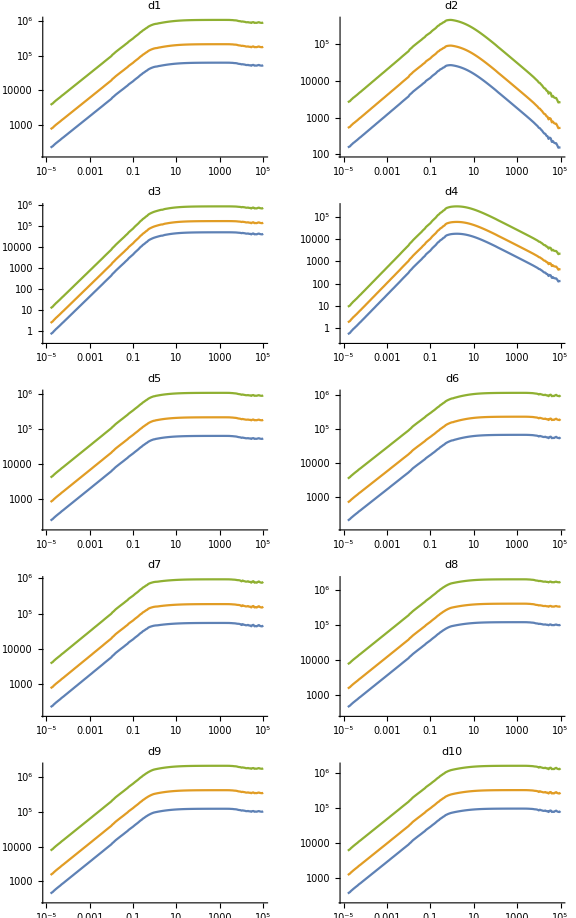

```mathematica
GraphicsGrid[Partition[SensPlots,2], ImageSize->Large ]
```